```mathematica
Quit[]
```

```mathematica
<<"../../../ltd_math_utils/LTDTools.m"
```

The documented functions in this package are: 
 ?plotGraph 
 ?findIsomorphicGraphs 
 ?constructCuts 
 ?importGraphs 
 ?getLoopLines 
 ?getCutStructure 
 ?writeMinimalJSON 
 ?extractTensCoeff 
 ?getSymCoeff 
 ?processNumerator 
 ?createSuperGraph 
 ?translateToFeynCalc 
 ?getSymCoeffSP
 ----------------------------------------- 
 Needs the package FeynCalc which can installed with Import["https://raw.githubusercontent.com/FeynCalc/feyncalc/master/install.m"]; InstallFeynCalc[]
 Needs the package IGraphM which can be downloaded from https://github.com/szhorvat/IGraphM. !!! 
 Run: Get["https://raw.githubusercontent.com/szhorvat/IGraphM/master/IGInstaller.m"] for installation.

FeynCalc 9.3.0 (stable version). For help, use the documentation center, check out the wiki or write to the mailing list.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, P3H-20-002, TTP19-020, TUM-EFT 130/19, arXiv:2001.04407

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207, 432-444, 2016, arXiv:1601.01167

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

```mathematica
allGraphs=importGraphs["./phot_qqb.qgr",sumIsoGraphs->False];
```

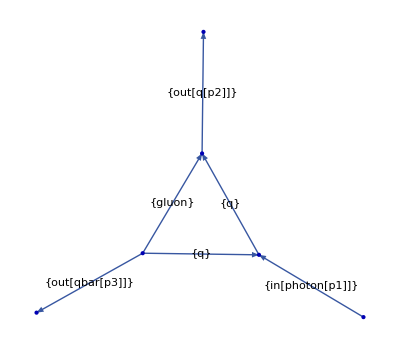

```mathematica
plotGraph[allGraphs,edgeLabels->{"particleType"}]
```

```mathematica
allGraphs=processNumerator[allGraphs,"./minFeynRulesQEDQCD.m",additionalRules->{p1->p2+p3,in[x__]:>1, out[x__]:>1,scalarProp[x__]:>1,ii->I}, extractTensors->True,symCoefficients->False,coeffFormat->"short",spinChainSimplify->True,spinSum->True];
```

```mathematica
ClearAll[uvNumerator1Loop]
uvNumerator1Loop[graph_]:=Block[{mygraph=graph,projectedNumerator,projector},
projector[myrank_,loopMomentum_]:=Block[{projec,ind,coeff,tens,g,projectedTensor},
If[OddQ[myrank],
Return[0]
];
SetAttributes[g,Orderless];
ind=Table[lMomInd[1][i],{i,myrank}];
tens=(DeleteDuplicates@(Times@@@(Apply[g,#,{1}]&/@(ArrayReshape[#,{2,2}]&/@Permutations[ind]))));
projec=translateToFeynCalc[(Inverse@(Contract[translateToFeynCalc[KroneckerProduct[tens,tens]]])).tens];
translateToFeynCalc[tens.(Contract[translateToFeynCalc[projec*(Product[vector[loopMomentum,i],{i,ind}])]])]
];
projectedNumerator=Plus@@(DiracSimplify@(Contract[Times[#[[2]],projector[#[[1,1]],graph[["loopMomenta",1]]]]&/@(mygraph[["analyticTensorCoeff"]])]));
mygraph=Append[mygraph,Association@("uv_numerator"->projectedNumerator)]
]
ClearAll[buildUVGraph]
buildUVGraph[graph_]:=Block[{uvgraph=graph},
uvgraph[["edges"]]=uvgraph[["edges"]]/. v[x_]:>v[1]//DeleteDuplicates;
uvgraph=Append[uvgraph,Association@("powers"->Join[ConstantArray[1,Length@Cases[uvgraph[["momentumMap"]],x_/;!FreeQ[x,Alternatives@@{out,in}],{1}]],
{Length@Cases[uvgraph[["momentumMap"]],x_/;FreeQ[x,Alternatives@@{out,in}],{1}]}])];
uvgraph[["momentumMap"]]=Join[Cases[uvgraph[["momentumMap"]],x_/;!FreeQ[x,Alternatives@@{out,in}],{1}],uvgraph[["loopMomenta"]]];
uvgraph[["particleType"]]=Join[Cases[uvgraph[["particleType"]],x_/;!FreeQ[x,Alternatives@@{out,in}],{1}],{uvScalar}];
uvgraph=uvNumerator1Loop[uvgraph];
uvgraph=KeyDrop[uvgraph,"numerator"];
uvgraph=KeyDrop[uvgraph,"analyticTensorCoeff"];
uvgraph=KeyDrop[uvgraph,"numerator_unevaluated"];

uvgraph=Append[uvgraph,Association@("name"->"uvCT_"<>((ToString/@Cases[uvgraph[["particleType"]],in[x_[y_]]:>x,Infinity])/. List[x___]:>StringJoin[x])<>"_"<>((ToString/@Cases[uvgraph[["particleType"]],out[x_[y_]]:>x,Infinity])/. List[x___]:>StringJoin[x]))];
uvgraph=Append[Association@("original_graph"->graph),Association@("uv_approximant"->uvgraph)]
]
```

```mathematica
buildAnalyticCT[graph_]:=Block[{mygraph=graph,analyticCT,topo,uvNumeratorAna=graph[["uv_approximant","uv_numerator"]],mUV,tadpole,ep,coeff},
coeff[pol_,x_Symbol]:=Simplify/@({#->Coefficient[pol,x,#]}&/@Exponent[pol,x,List]);
tadpole[m_,n_,d_]:=I Pi^(d/2)/(2 Pi)^d(-1)^n Gamma[n+ep-2]/Gamma[n] 1/((m^2)^(n+ep-2));
uvNumeratorAna=topo[1]^graph[["uv_approximant","powers",-1]]*(uvNumeratorAna/.Pair[Momentum[graph[["uv_approximant","loopMomenta",1]],D],Momentum[graph[["uv_approximant","loopMomenta",1]],D]]-> topo[-1]+mUV^2 )//Expand;
topo[a_]^b_^:=topo[a*b];
topo[a_]topo[b_]^:=topo[a+b];
uvNumeratorAna=Association@(coeff[Series[(uvNumeratorAna/. LorentzIndex[a_,D]:>LorentzIndex[a]/.D->4-2ep/.topo[a_]:>tadpole[mUV,a,4-2ep]),{ep,0,0}]//Normal,ep]);
mygraph=Append[mygraph[["uv_approximant"]],Association@("analytic_uv_ct"->uvNumeratorAna)]
]
```

```mathematica
buildAnalyticCT[buildUVGraph[allGraphs]]
```

<|edges→{in[1]→v[1],v[1]→out[1],v[1]→out[2],v[1]→v[1]},particleType→{in[photon[p1]],out[q[p2]],out[qbar[p3]],uvScalar},momentumMap→{in[p1],out[p2],out[p3],k1},loopMomenta→{k1},powers→{1,1,1,3},uv_numerator→-4 CF ee gs^2 charge[q] DiracChain[DiracGamma[LorentzIndex[mu[-1],D],D],DiracIndex[s[-2]],DiracIndex[s[-4]]] Pair[Momentum[k1,D],Momentum[k1,D]] SUNFDelta[SUNFIndex[sunF[-4]],SUNFIndex[sunF[-2]]]+1/D 4 CF ee gs^2 charge[q] DiracChain[DiracGamma[LorentzIndex[mu[-1],D],D],DiracIndex[s[-2]],DiracIndex[s[-4]]] Pair[Momentum[k1,D],Momentum[k1,D]] SUNFDelta[SUNFIndex[sunF[-4]],SUNFIndex[sunF[-2]]]+CF D ee gs^2 charge[q] DiracChain[DiracGamma[LorentzIndex[mu[-1],D],D],DiracIndex[s[-2]],DiracIndex[s[-4]]] Pair[Momentum[k1,D],Momentum[k1,D]] SUNFDelta[SUNFIndex[sunF[-4]],SUNFIndex[sunF[-2]]],name→uvCT_photon_qqbar,analytic_uv_ct→<|-1→(ⅈ CF ee gs^2 charge[q] DiracChain[DiracGamma[LorentzIndex[mu[-1]]],DiracIndex[s[-2]],DiracIndex[s[-4]]] SUNFDelta[SUNFIndex[sunF[-4]],SUNFIndex[sunF[-2]]])/(16 π^2),0→-(ⅈ CF ee gs^2 charge[q] DiracChain[DiracGamma[LorentzIndex[mu[-1]]],DiracIndex[s[-2]],DiracIndex[s[-4]]] (2+EulerGamma+Log[mUV^2/(4 π)]) SUNFDelta[SUNFIndex[sunF[-4]],SUNFIndex[sunF[-2]]])/(16 π^2)|>|>

```mathematica
FourDivergence[allGraphs[["numerator"]],Pair[LorentzIndex[a,D],Momentum[p2,D]]]
```

CF ee gs^2 charge[q] DiracChain[1,DiracIndex[s[-2]],DiracIndex[s[-4]]] (2 DiracGamma[LorentzIndex[a,D],D].DiracGamma[LorentzIndex[mu[-1],D],D].DiracGamma[Momentum[k1,D],D]-4 DiracGamma[Momentum[k1,D],D].DiracGamma[LorentzIndex[mu[-1],D],D].DiracGamma[LorentzIndex[a,D],D]+D DiracGamma[Momentum[k1,D],D].DiracGamma[LorentzIndex[mu[-1],D],D].DiracGamma[LorentzIndex[a,D],D]) SUNFDelta[SUNFIndex[sunF[-4]],SUNFIndex[sunF[-2]]]

```mathematica
translateToFeynCalc[vector[p,a]]
```

Pair[LorentzIndex[a,D],Momentum[p,D]]

```mathematica
multiTaylor[f_,{vars_?VectorQ,pt_?VectorQ,n_Integer?NonNegative}]:=Sum[Nest[(vars-pt).#&,(D[f,{vars,k}]/.Thread[vars->pt]),k]/k!,{k,0,n},Method->"Procedural"]
```

```mathematica
multiTaylor[f[x,y,z],{{x,y,z},{pref1,pref2,pref3},3}]
```

f[pref1,pref2,pref3]+(-pref3+z) f^(0,0,1)[pref1,pref2,pref3]+(-pref2+y) f^(0,1,0)[pref1,pref2,pref3]+(-pref1+x) f^(1,0,0)[pref1,pref2,pref3]+1/2 ((-pref3+z) ((-pref3+z) f^(0,0,2)[pref1,pref2,pref3]+(-pref2+y) f^(0,1,1)[pref1,pref2,pref3]+(-pref1+x) f^(1,0,1)[pref1,pref2,pref3])+(-pref2+y) ((-pref3+z) f^(0,1,1)[pref1,pref2,pref3]+(-pref2+y) f^(0,2,0)[pref1,pref2,pref3]+(-pref1+x) f^(1,1,0)[pref1,pref2,pref3])+(-pref1+x) ((-pref3+z) f^(1,0,1)[pref1,pref2,pref3]+(-pref2+y) f^(1,1,0)[pref1,pref2,pref3]+(-pref1+x) f^(2,0,0)[pref1,pref2,pref3]))+1/6 ((-pref3+z) ((-pref3+z) ((-pref3+z) f^(0,0,3)[pref1,pref2,pref3]+(-pref2+y) f^(0,1,2)[pref1,pref2,pref3]+(-pref1+x) f^(1,0,2)[pref1,pref2,pref3])+(-pref2+y) ((-pref3+z) f^(0,1,2)[pref1,pref2,pref3]+(-pref2+y) f^(0,2,1)[pref1,pref2,pref3]+(-pref1+x) f^(1,1,1)[pref1,pref2,pref3])+(-pref1+x) ((-pref3+z) f^(1,0,2)[pref1,pref2,pref3]+(-pref2+y) f^(1,1,1)[pref1,pref2,pref3]+(-pref1+x) f^(2,0,1)[pref1,pref2,pref3]))+(-pref2+y) ((-pref3+z) ((-pref3+z) f^(0,1,2)[pref1,pref2,pref3]+(-pref2+y) f^(0,2,1)[pref1,pref2,pref3]+(-pref1+x) f^(1,1,1)[pref1,pref2,pref3])+(-pref2+y) ((-pref3+z) f^(0,2,1)[pref1,pref2,pref3]+(-pref2+y) f^(0,3,0)[pref1,pref2,pref3]+(-pref1+x) f^(1,2,0)[pref1,pref2,pref3])+(-pref1+x) ((-pref3+z) f^(1,1,1)[pref1,pref2,pref3]+(-pref2+y) f^(1,2,0)[pref1,pref2,pref3]+(-pref1+x) f^(2,1,0)[pref1,pref2,pref3]))+(-pref1+x) ((-pref3+z) ((-pref3+z) f^(1,0,2)[pref1,pref2,pref3]+(-pref2+y) f^(1,1,1)[pref1,pref2,pref3]+(-pref1+x) f^(2,0,1)[pref1,pref2,pref3])+(-pref2+y) ((-pref3+z) f^(1,1,1)[pref1,pref2,pref3]+(-pref2+y) f^(1,2,0)[pref1,pref2,pref3]+(-pref1+x) f^(2,1,0)[pref1,pref2,pref3])+(-pref1+x) ((-pref3+z) f^(2,0,1)[pref1,pref2,pref3]+(-pref2+y) f^(2,1,0)[pref1,pref2,pref3]+(-pref1+x) f^(3,0,0)[pref1,pref2,pref3])))

```mathematica
allGraphs["numerator"]//Simplify//TraditionalForm
```

ee gs^2 C_F charge(q) δ_(sunF(-4)sunF(-2)) ((D-4) ((γ·k1).γ^(mu(-1)).(γ·p2))_(s(-2)s(-4))+(D-4) ((γ·k1).γ^(mu(-1)).(γ·p3))_(s(-2)s(-4))+D k1^2 (γ^(mu(-1)))_(s(-2)s(-4))-2 D k1^(mu(-1)) (γ·k1)_(s(-2)s(-4))+2 ((γ·p2).γ^(mu(-1)).(γ·k1))_(s(-2)s(-4))+2 ((γ·p3).γ^(mu(-1)).(γ·k1))_(s(-2)s(-4))-2 k1^2 (γ^(mu(-1)))_(s(-2)s(-4))+4 k1^(mu(-1)) (γ·k1)_(s(-2)s(-4)))